# Silicon qubit device in the university of Delft

reference: https://arxiv.org/abs/2202.09252
scientific contributor: Fernando

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Connectivity of this device

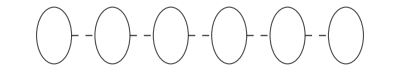

```mathematica
nodes=Labeled[#,Placed[{#,"Q"<>ToString[#+1]},{Below,Center}]]&/@Range[0,5];
Graph[nodes,Table[j<->j+1,{j,nodes[[All,1]][[;;-2]]}],VertexSize->0.6,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{11,FontFamily->"Serif"},ImageSize->Automatic,EdgeStyle->Directive[Black,Thick,Dashed]]
```

Set the default configuration of the device

```mathematica
Options[SiliconDelft]={
QubitNum->6,
(*average of T1*)
T1->10^4,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs. We assume the T2* is echoed out to T2 *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(*rabi frequencies on single rotations: 5 is average *)
RabiFreq-><|0->5,1->5,2->5,3->5,4->5,5->5|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->True,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,
(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors. Keys are the smallest qubit number. This applies to C[Ph] gates *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9374945614729504,1->0.9339691831083574,2->0.9286379436705322,3->0.9967228426036524,4->0.9793017377403548|>,
(* CROT/Controlled-X rotation *)
FidCRot->0.9988,
(* Rabi frequency of CROT in MHz, conditional microwave drive *)
FreqCRot->5,
(* Error fraction/ratio {depolarising, dephasing} of controled-Ph(π) rotation or controlled-Z. The error for other θ is scalled from π. *)
EFCZ->{0,1},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,
(* Parity readout fidelity/charge readout fidelity, on 01 and 56. 2-qubit readout error: 2-qubit bitflip *)
FidRead->0.9997,
(*Parity readout duration in μs *)
DurRead->10
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[X_j], C_i[Ph_j[θ]],  Read, Init,  Wait_i[Δt]

## The noise model and basic operations

```mathematica
ψ=CreateQureg[6];
ρ=CreateDensityQureg[6];
```

Remarks: the time unit is μs

### Passive noise

The passive noise when no gates are applied.
The noise forms:
1) Cross-talk C_i[Rz_(i+1)(Δt)]  from input ExchangeRotOff, which is exchange rotation when no C[Z] gate is applied. 
2) Standard dephasing from T2 input and depolarising from T1 inputs. We assume the T2* is echoed out to T2

The standard passivenoise (2) can be eliminated by setting StdPassiveNoise -> False. The Cross-talk (1) can be set off by setting ExchangeRotOff->False

{{0,{C_0[Rz_1[0.039]],Deph_0[0.100502],Depol_0[0.000235582]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.015]],Deph_1[0.0691683],Depol_1[0.000235582],C_2[Rz_3[0.03]],Deph_2[0.0376768],Depol_2[0.000235582],C_3[Rz_4[0.02]],Deph_3[0.0404918],Depol_3[0.000235582],C_4[Rz_5[0.028]],Deph_4[0.0339344],Depol_4[0.000235582],Deph_5[0.055502],Depol_5[0.000235582]}}}

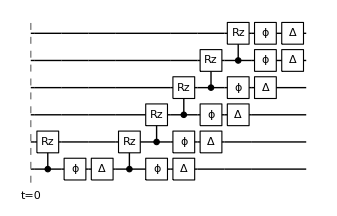

```mathematica
InsertCircuitNoise[{Subscript[Wait, 0][π]},SiliconDelft[]]
DrawCircuit[%]
```

### Single qubit gates

Single qubit gates: x- and y- rotations have the same error 
The noise forms:
1) Off-resonant Rabi Oscillation. This takes RabiFreq input and applied when OffResonantRabi->True.
2) Standard Dephasing and Depolarising noise. This takes FidSingleXY and EFSingleXY inputs to estimate the error parameters. Set EFSingleXY->{0,0} to set this off.

{{0,{Rx_0[π/2],Depol_0[0.],Deph_0[0.001725],U_1[{{0.999287-0.0377401 ⅈ,-1.35127×10^-17-0.000725771 ⅈ},{-1.35127×10^-17-0.000725771 ⅈ,0.999287+0.0377401 ⅈ}}],U_2[{{0.999896-0.0144364 ⅈ,-1.45569×10^-18-0.00010615 ⅈ},{-1.45569×10^-18-0.00010615 ⅈ,0.999896+0.0144364 ⅈ}}],U_3[{{0.999791-0.02045 ⅈ,3.05645×10^-16-0.000213021 ⅈ},{3.05645×10^-16-0.000213021 ⅈ,0.999791+0.02045 ⅈ}}],U_4[{{0.999385-0.0350469 ⅈ,-9.81184×10^-18-0.000625837 ⅈ},{-9.81184×10^-18-0.000625837 ⅈ,0.999385+0.0350469 ⅈ}}],U_5[{{0.98769-0.139614 ⅈ,0.0705493-2.76517×10^-16 ⅈ},{0.0705493-2.76517×10^-16 ⅈ,-0.98769-0.139614 ⅈ}}]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.0015]],Deph_1[0.00738939],Depol_1[0.0000235616],C_2[Rz_3[0.003]],Deph_2[0.00390189],Depol_2[0.0000235616],C_3[Rz_4[0.002]],Deph_3[0.00420479],Depol_3[0.0000235616],C_4[Rz_5[0.0028]],Deph_4[0.00350177],Depol_4[0.0000235616],Deph_5[0.00584866],Depol_5[0.0000235616]}},{π/10,{C_0[Rz_1[0.0124141]],Deph_0[0.0344686],Depol_0[0.0000749963]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.00477465]],Deph_1[0.0231439],Depol_1[0.0000749963],C_2[Rz_3[0.0095493]],Deph_2[0.0123146],Depol_2[0.0000749963],C_3[Rz_4[0.0063662]],Deph_3[0.0132618],Depol_3[0.0000749963],C_4[Rz_5[0.00891268]],Deph_4[0.0110615],Depol_4[0.0000749963],Deph_5[0.0183802],Depol_5[0.0000749963]}}}

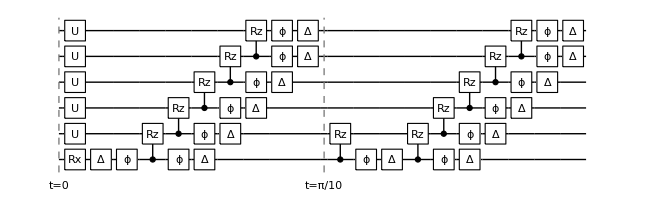

```mathematica
InsertCircuitNoise[CircSiliconDelft[{Subscript[Rx, 0][π/2],Subscript[Wait, 0][1]}, Parallel->False],SiliconDelft[StdPassiveNoise->True,OffResonantRabi->True]]
DrawCircuit[%]
```

#### Controlled - Z, Coltrolled-Phase

The noisy forms:
1) Standard 2-qubits dephasing and depolarising noise. This takes information FidCZ (fidelities) and EFCZ (error fraction). Set it off by EFCZ->{0,0}
2) Exchange rotation when C-Z is on. Takes information ExchangeRotOn. Set ExchangeRotOn -> False to set it off.

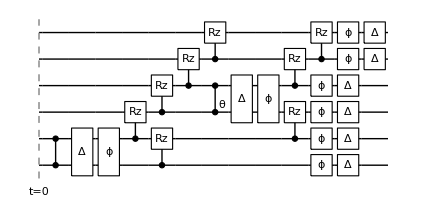

```mathematica
InsertCircuitNoise[{Subscript[C, 0][Subscript[Z, 1]],Subscript[C, 2][Subscript[Ph, 3][θ]]},SiliconDelft[StdPassiveNoise->True,EFCZ->{0,0}]];
DrawCircuit[%]
```

{{0,{C_1[X_0],Depol_(1,0)[0.0012]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.]],Deph_1[0.],Depol_1[0.],C_2[Rz_3[0.00190986]],Deph_2[0.00248756],Depol_2[0.0000149999],C_3[Rz_4[0.00127324]],Deph_3[0.00268096],Depol_3[0.0000149999],C_4[Rz_5[0.00178254]],Deph_4[0.00223214],Depol_4[0.0000149999],Deph_5[0.00373133],Depol_5[0.0000149999]}}}

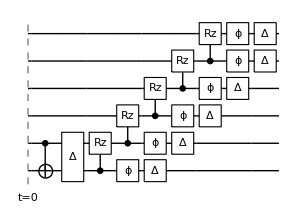

```mathematica
InsertCircuitNoise[{Subscript[CRot, 1,0]},SiliconDelft[],ReplaceAliases->True]
DrawCircuit[%]
```

### Readout: parity measurement

{{0,{Kraus_(1,0)[{{{0.99985,0.,0.,0.},{0.,0.99985,0.,0.},{0.,0.,0.99985,0.},{0.,0.,0.,0.99985}},{{0.,0.01,0.,0.},{0.01,0.,0.,0.},{0.,0.,0.,0.01},{0.,0.,0.01,0.}},{{0.,0.,0.01,0.},{0.,0.,0.,0.01},{0.01,0.,0.,0.},{0.,0.01,0.,0.}},{{0.,0.,0.,0.01},{0.,0.,0.01,0.},{0.,0.01,0.,0.},{0.01,0.,0.,0.}}}],Damp_6[1],X_6,H_6,C_6[Z_1],C_6[Z_0],H_6,M_6,Kraus_(1,0)[{{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}}}],Kraus_(1,0)[{{{0.99985,0.,0.,0.},{0.,0.99985,0.,0.},{0.,0.,0.99985,0.},{0.,0.,0.,0.99985}},{{0.,0.01,0.,0.},{0.01,0.,0.,0.},{0.,0.,0.,0.01},{0.,0.,0.01,0.}},{{0.,0.,0.01,0.},{0.,0.,0.,0.01},{0.01,0.,0.,0.},{0.,0.01,0.,0.}},{{0.,0.,0.,0.01},{0.,0.,0.01,0.},{0.,0.01,0.,0.},{0.01,0.,0.,0.}}}]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.]],Deph_1[0.],Depol_1[0.],C_2[Rz_3[0.095493]],Deph_2[0.110357],Depol_2[0.000749625],C_3[Rz_4[0.063662]],Deph_3[0.117859],Depol_3[0.000749625],C_4[Rz_5[0.0891268]],Deph_4[0.100228],Depol_4[0.000749625],Deph_5[0.156194],Depol_5[0.000749625]}}}

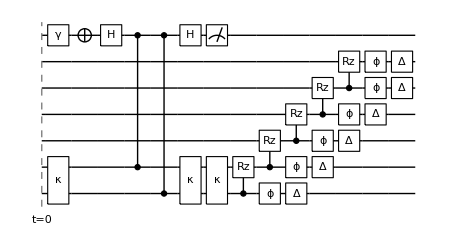

```mathematica
InsertCircuitNoise[{Subscript[MeasP, 1,0]},SiliconDelft[],ReplaceAliases->True]
DrawCircuit[%]
```

## Reproducing results from the paper

Initialisation is obtained by 2 readouts and a partial swap with single qubit errors
The qubits are initialised to state 100 ... 001

### Realtime feedback initialisation to 10 and 100

```mathematica
ρ=CreateDensityQureg[7];
```

```mathematica
(* initialisation done in the paper *)
SetAttributes[readInit,HoldFirst]
readInit[ρ_,q0_,q1_,opt_:{}]:=Module[{m1,m2},
m1=First@Flatten@ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[MeasP, q0,q1]},SiliconDelft[Sequence@@opt],ReplaceAliases->True]];
If[m1==1,ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[Rx, q0][π]},SiliconDelft[Sequence@@opt],ReplaceAliases->True]]];
m2=First@Flatten@ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[MeasP, q0,q1]},SiliconDelft[Sequence@@opt],ReplaceAliases->True]];
{m1,m2}
]

(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[7]];
readInit[ρ,0,1]
Re@PartialTrace[ρ,2,3,4,5,6][[2,2]]
```

{1,0}

0.9997

```mathematica
(*Initialisation and (QND on q2) to 100: 
works when the output of last parity measurement is zero. When the last output is one, repeat the process *)
readInit3[ρ_,q0_,q1_,q2_,opt_:{}]:=Module[{m1,m2,m3},
m1=First@Flatten@ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[MeasP, q0,q1]},SiliconDelft[Sequence@@opt],ReplaceAliases->True]];
If[m1==1,ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[Rx, q0][π]},SiliconDelft[Sequence@@opt],ReplaceAliases->True]]];
m2=First@Flatten@ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[MeasP, q0,q1]},SiliconDelft[Sequence@@opt],ReplaceAliases->True]];
m3=First@Flatten@ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[CRot, q2,q1],Subscript[MeasP, q0,q1]},SiliconDelft[Sequence@@opt],ReplaceAliases->True]];
If[m3==1,ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[Rx, q2][π]},SiliconDelft[Sequence@@opt],ReplaceAliases->True]]];
{m1,m2,m3}
]
```

```mathematica
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[7]];
```

```mathematica
readInit3[ρ,0,1,2]
Re@PartialTrace[ρ,3,4,5,6][[2,2]]
```

{0,0,0}

0.998004

```mathematica
readInit3[ρ,5,4,3]
Re@PartialTrace[ρ,0,1,2,6][[5,5]]
```

{1,0,0}

0.997849

### Full device initialisation to 100001: quoted value 95

```mathematica
ψ5=CreateQureg[7];
ApplyCircuit[InitZeroState@ψ5,{Subscript[X, 0],Subscript[X, 5]}];
```

```mathematica
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[7]];
repeat=4;

opt={};
Table[readInit3[ρ,5,4,3,opt],{repeat}]
Table[readInit3[ρ,0,1,2,opt],{repeat}]
CalcFidelity[ρ,ψ5]
```

{{0,0,1},{1,0,0},{0,0,0},{0,0,0}}

{{1,0,0},{0,0,1},{1,0,0},{0,0,0}}

0.978784

### Obtaining T1: X180-τ- with perfect measurement

```mathematica
RelaxationExperiment[dev_,qubit_,initrep_:2]:=Module[{init},
Table[
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[7]];
Table[readInit3[ρ,5,4,3],{initrep}];
Table[readInit3[ρ,0,1,2],{initrep}];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[If[MemberQ[{0,5},qubit],{Subscript[Wait, 0][t]},List/@{Subscript[Rx, qubit][π],Subscript[Wait, 0][t]},dev],dev]];
{t,CalcProbOfOutcome[ρ,qubit,1]},{t,0,10^4,1000}]
]
```

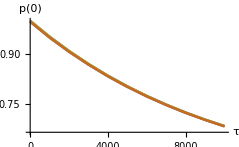

```mathematica
ListPlot[RelaxationExperiment[SiliconDelft[],#]&/@Range[0,5],PlotLegends->Range[0,5],Joined->True,ImageSize->200,AxesLabel->{"τ","p(0)"}]
```

### Obtaining T_2 : X90 - tau - X180 - tau - X90, tau = 1 μs

```mathematica
HahnEchoExperiment[dev_,qubit_,initrep_:2]:=Module[{},
Table[
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[7]];
Table[readInit3[ρ,5,4,3],{initrep}];
Table[readInit3[ρ,0,1,2],{initrep}];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[List/@{Subscript[Rx, qubit][π/2],Subscript[Wait, 0][t/2],Subscript[Rx, qubit][π],Subscript[Wait, 0][t/2],Subscript[Rx, qubit][π/2]},dev]];
{t,CalcProbOfOutcome[ρ,qubit,If[MemberQ[{5,0},qubit],1,0]]},{t,0,60,4}]
]
```

```mathematica
OptionValue[SiliconDelft,T2]
```

<|0→14,1→21.1,2→40.1,3→37.2,4→44.7,5→26.7|>

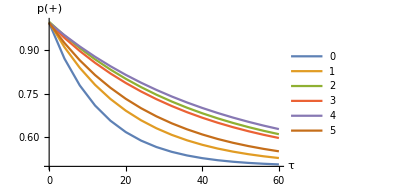

```mathematica
ListPlot[HahnEchoExperiment[SiliconDelft[],#]&/@Range[0,5],PlotLegends->Range[0,5],PlotRange->{0.5,1},Joined->True,ImageSize->300,AxesLabel->{"τ","p(+)"}]
```

```mathematica
(*ideal plot to the Total wait time t/2*)
(*Plot[(1+ⅇ^(-x/#))/2&/@Values@OptionValue[SiliconDelft,T2],{x,0,60},PlotRange->{0.5,1},ImageSize->300]*)
```

## Paper supplement: Bell states

```mathematica
chartstyle[label_]:={ImageSize->200,BarSpacing->0.1,ColorFunction->Function[{height},If[height<0.1,ColorData["Rainbow"][10height],ColorData["DeepSeaColors"][(height-0.9)*10]]],ChartElementFunction->"Cube",ChartStyle->EdgeForm[Thick],PlotTheme->"Business",Ticks->{{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},Automatic},LabelStyle->Directive[Bold,Black],
Epilog->Inset[Style[label,Thick,17],ImageScaled[{.2,.7}]],PlotRange->All
};
```

The CZ gates’ fidelities are unknown. We set it according to the results on the Bell states fidelity.

```mathematica
ψ2=CreateQureg[2];
ρ2=CreateDensityQureg[2];
```

```mathematica
concurence[ρ_]:=Module[{eigv,ρm,ρms,ρt,nq,pauliy},
ρm=GetQuregMatrix@ρ;
nq=IntegerPart@Log2@Length@ρm;
ρms=MatrixPower[ρm,1/2];
pauliy=CalcCircuitMatrix[Subscript[Y, #]&/@Range[0,nq-1]];
ρt=pauliy.Conjugate[ρm].pauliy;
eigv=Reverse@Sort[Chop@Eigenvalues[MatrixPower[ρms.ρt.ρms,1/2]]];
Max[0,eigv[[1]]-Total@eigv[[2;;]]]
]
```

```mathematica
bellcircρ=<|
"01"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},
"12"->{Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]},
"23"->{Subscript[Rx, 2][π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][π/2]},
"34"->{Subscript[Rx, 3][π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][π/2]},
"45"->{Subscript[Rx, 4][π/2],Subscript[Rx, 5][π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][π/2]}|>;
bellcircψ=<|
"01"->{Subscript[X, 0],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},
"12"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},
"23"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},
"34"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},
"45"->{Subscript[X, 1],Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]}|>;
```

```mathematica
bell[code_,opt_,initrep_:4]:=Module[{qubits,fid,plot,conc,str},
qubits=ToExpression@StringSplit[code,""];

SetQuregMatrix[ρ,RandomMixState[7]];
Table[readInit3[ρ,5,4,3,opt],{initrep}];
Table[readInit3[ρ,0,1,2,opt],{initrep}];

ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Serialize@{bellcircρ[code]},SiliconDelft[Sequence@@opt]]];
SetQuregMatrix[ρ2,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits],6]];
conc=concurence[ρ2]*100;
ApplyCircuit[InitZeroState@ψ2,bellcircψ[code]];
fid=CalcFidelity[ρ2,ψ2]*100;
str="Q"<>ToString[1+qubits[[1]]]<>"-Q"<>ToString[1+qubits[[2]]];
plot=PlotDensityMatrix[ρ2,ψ2,Sequence@@chartstyle[str]];
{str,plot,fid,conc}
]
```

-Graphics-

```mathematica
plots=Transpose[bell[#,{},4]&/@ReplaceList[Sort@Range[0,5],{p___,a_,b_,q___}:>StringRiffle[{a,b},""]]];
TableForm[Transpose@{DecimalForm[#,4]&/@plots[[3]],DecimalForm[#,4]&/@plots[[4]]},TableHeadings->{plots[[1]],{"Fidelity","Concurence"}}]
Row@plots[[2]]
```

| Fidelity | Concurence
Q1-Q2 | 89.4 | 79.75
Q2-Q3 | 90.18 | 80.42
Q3-Q4 | 88.7 | 79.07
Q4-Q5 | 95.96 | 94.48
Q5-Q6 | 94.27 | 90.6

-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-

```mathematica
Table[
  Export["~/vqd/img/" <> plots[[1, i]] <> ".pdf", plots[[2, i]]],
  {i, Length@plots[[1]]}]
```

{~/vqd/img/Q1-Q2.pdf,~/vqd/img/Q2-Q3.pdf,~/vqd/img/Q3-Q4.pdf,~/vqd/img/Q4-Q5.pdf,~/vqd/img/Q5-Q6.pdf}

```mathematica
Round[#,0.01]&/@plots[[3]]
Mean@%
```

{89.4,90.18,88.71,95.98,94.32}

91.718

### 3 - qubits GHZ: todo

```mathematica
ψ3=CreateQureg[3];
ρ3=CreateDensityQureg[3];
```

```mathematica
ghzcircρ=<|
"012"->{Subscript[Rx, 0][-π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},
"123"->{Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][-π/2]},
"234"->{Subscript[Rx, 2][π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][-π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][-π/2]},
"345"->{Subscript[Rx, 3][π/2],Subscript[Rx, 4][-π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][π/2],Subscript[Rx, 5][π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][π/2]}
|>;
ghzcircψ=<|
"012"->Join[{Subscript[X, 0]},ghzcircρ["012"]],
"123"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},
"234"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},
"345"->{Subscript[X, 2],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]}
|>;
ghz[code_,opt_,initrep_:2]:=Module[{qubits,fid,plot,str},
qubits=ToExpression@StringSplit[code,""];

SetQuregMatrix[ρ,RandomMixState[7]];
Table[readInit3[ρ,5,4,3,opt],{initrep}];
Table[readInit3[ρ,0,1,2,opt],{initrep}];

SetQuregMatrix[ρ,RandomMixState[7]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[Serialize@{ghzcircρ[code]},SiliconDelft[Sequence@@opt]]];
SetQuregMatrix[ρ3,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits],6]];
ApplyCircuit[InitZeroState@ψ3,ghzcircψ[code]];
fid=100*CalcFidelity[ρ3,ψ3];
str="Q"<>ToString[1+qubits[[1]]]<>"-Q"<>ToString[1+qubits[[2]]]<>"-Q"<>ToString[1+qubits[[3]]];
plot=PlotDensityMatrix[ρ3,ψ3,Sequence@@chartstyle[str]];
{plot,"F_est("<>StringRiffle[qubits+1,"-"]<>")="<>ToString@fid}
]
```

## Quantum Fourier Transform: manual translation

Basic gate using the native gates: phase, controlled-phase, hadamard, swap

```mathematica
Subscript[sw, a_,b_]:=Sequence@@{Subscript[H, a],Subscript[C, a][Subscript[Z, b]],Subscript[H, a],Subscript[H, b],Subscript[C, a][Subscript[Z, b]],Subscript[H, b],Subscript[H, a],Subscript[C, a][Subscript[Z, b]],Subscript[H, a]}
```

```mathematica
connectivity[nq_]:=Graph[Table[i<->i+1,{i,0,nq-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

```mathematica
qft2native={
(*Subscript[C, a_][Subscript[Ph, b_][θ_]]:>Sequence@@{Subscript[Rx, b][-π/2],Subscript[Ry, b][θ/2],Subscript[Rx, b][-π/2],Subscript[Ry, b][-π/2],Subscript[C, a][Subscript[Z, b]],Subscript[Rx, 1][-θ/2],Subscript[C, a][Subscript[Z, b]],Subscript[Rx, b][π],Subscript[Ry, b][-π/2],Subscript[Rx, a][-π/2],Subscript[Ry, a][θ/2],Subscript[Rx, a][π/2],G[θ/4]},*)
Subscript[H, a_]:>Sequence@@{Subscript[Rx, 0][π],Subscript[Ry, 0][-π/2],G[π/2]},
Subscript[C, a_][Subscript[Ph, b_][θ_]]:>Subscript[C, a][Subscript[Ph, b][θ]],
Subscript[Ph, a_][θ_]:>Sequence@@{Subscript[Rx, a][-π/2],Subscript[Ry, a][θ],Subscript[Rx, a][π/2],G[θ/2]}
};
```

```mathematica
Subscript[cph, i_,j_][θ_,nq_]:=Module[{qs,circ},
qs=ReplaceList[FindShortestPath[connectivity[nq],i,j],{p___,a_,b_,q___}:>{a,b}];
Sequence@@Flatten@{Subscript[C, qs[[1,1]]][Subscript[Ph, qs[[1,2]]][θ]],Subscript[SWAP, #[[1]],#[[2]]]&/@qs[[2;;]]}
]
```